```mathematica
Manipulate[ParametricPlot[{-Sin[t],A Sin[t-0.1]},{t,-π,π},PlotStyle->{Red, Dashed},PlotRange->{-1,1}],{A,0,1}]
```

```mathematica
E1=0.0534;      (* 10^14 W/cm^2 *)
ω=0.057;          (* 800nm *)
nc=5;
Subscript[E, 800][t_]:=E1 (Sin[(ω t)/(2 nc)])^2 Cos[ω t];
(*ListLinePlot[Table[Subscript[E, 800][t],{t,-1000,1000}],DataRange->{-1000,1000},PlotStyle->{Dot,Red}]*)
σ=8*41.34;    (* FWHM of Gauss pulse *)
Subscript[E, ωx][t_,ϕ_,ϵ_]:=1/(√(1+ϵ^2))E1 Exp[-4Log[2](t/σ)^2]Cos[ω t+ϕ];
Subscript[E, ωz][t_,ϕ_,ϵ_]:=ϵ/(√(1+ϵ^2))E1 Exp[-4Log[2](t/σ)^2]Sin[ω t+ϕ];
Subscript[E, 2ωx][t_,ϕ_,ϵ_,τ_,k_]:=1/(√(1+ϵ^2))√k E1 Exp[-4Log[2]((t-τ)/σ)^2]Cos[2ω t+2ϕ];
Subscript[E, 2ωz][t_,ϕ_,ϵ_,τ_,k_]:=ϵ/(√(1+ϵ^2))√k E1 Exp[-4Log[2]((t-τ)/σ)^2]Sin[2ω t+2ϕ];
(*Plot[Subscript[E, ωx][t],{t,-800,800},PlotStyle->{Dot,Red},PlotRange->All]*)
Manipulate[ListPointPlot3D[{Table[{Subscript[E, ωx][t,ϕ,ϵ]+Subscript[E, 2ωx][t,ϕ,ϵ,τ,k],t,Subscript[E, ωz][t,ϕ,ϵ]-Subscript[E, 2ωz][t,ϕ,ϵ,τ,k]},{t,-800,800,0.5}],Table[{0,t,Subscript[E, ωz][t,ϕ,ϵ]-Subscript[E, 2ωz][t,ϕ,ϵ,τ,k]},{t,-800,800,0.5}],Table[{Subscript[E, ωx][t,ϕ,ϵ]+Subscript[E, 2ωx][t,ϕ,ϵ,τ,k],t,0},{t,-800,800,0.5}]},ImageSize->Large,Axes->True,PlotStyle->{Red,Green,Blue},PlotRange->All,BoxRatios->{0.5, 1.5, 0.5}],{ϵ,1,0},{k,1,0},{ϕ,-π,π},{τ,0,1000}]
```

```mathematica
Manipulate[ListPlot[Table[{Subscript[E, ωx][t,ϕ,ϵ]+Subscript[E, 2ωx][t,ϕ,ϵ,τ,k],Subscript[E, ωz][t,ϕ,ϵ]-Subscript[E, 2ωz][t,ϕ,ϵ,τ,k]},{t,-500,1500,1}],PlotStyle->{Red,Dot},PlotRange->All,Joined->True],{ϵ,1,0},{k,1,0},{ϕ,-π,π},{τ,0,400}]
```

```mathematica
Manipulate[ListPlot[Table[{Subscript[E, ωx][t,ϕ,ϵ]+Subscript[E, 2ωx][t,ϕ,ϵ,τ,k],Subscript[E, ωz][t,ϕ,ϵ]+Subscript[E, 2ωz][t,ϕ,ϵ,τ,k]},{t,-500,1500,0.7}],PlotStyle->{Red,Dot},PlotRange->All,Joined->True],{ϵ,1,0},{k,1,0},{ϕ,-π,π},{τ,0,400}]
```

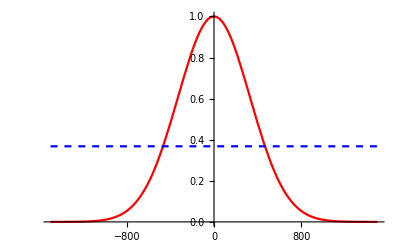

```mathematica
t0=0;
Plot[{Exp[(-(t-t0)^2)/(2 σ^2)],1/E},{t,-1500,1500},PlotStyle->{{Dot,Red},{Dashed,Blue}}]
```

```mathematica
Solve[(Exp[(-4 x^2)/σ^2])==1/E,x]
Solve[(Exp[-y^2/(2 σ^2)])^2==1/E,y]
Solve[Exp[-4Log[2]((t-t0)/σ)^2]==1/2,t](*光强*)……
Solve[Exp[-2Log[2]((t-t0)/σ)^2]==1/2,t](*电场,采用此种形式构造电场脉冲包络*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-165.36},{x→165.36}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→-330.72},{y→330.72}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-165.36},{t→165.36}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-233.854},{t→233.854}}

```mathematica
ListPointPlot3D[{Table[{Subscript[E, ωx][t,0,1]+Subscript[E, 2ωx][t,0,1,0,1],t,Subscript[E, ωz][t,0,1]+Subscript[E, 2ωz][t,0,1,0,1]},{t,-800,800,0.5}],Table[{0,t,Subscript[E, ωz][t,0,1]+Subscript[E, 2ωz][t,0,1,0,1]},{t,-800,800,0.5}],Table[{Subscript[E, ωx][t,0,1]+Subscript[E, 2ωx][t,0,1,0,1],t,0},{t,-800,800,0.5}]},ImageSize->Large,Axes->False,PlotStyle->{Red,Green,Blue},PlotRange->All,BoxRatios->{0.5, 1.5, 0.5},Boxed->False]
```

-Graphics3D-

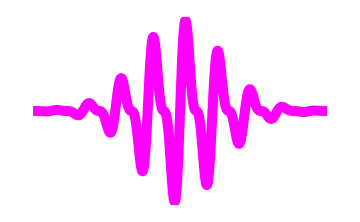

```mathematica
ListLinePlot[Table[Subscript[E, ωz][t,0,1]+Subscript[E, 2ωz][t,0,1,0,0.23],{t,-500,500,0.5}],Axes->False,PlotStyle->{Magenta,Thickness[0.02]},PlotRange->All,ImageSize->Medium]
```

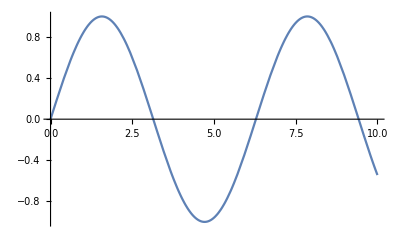

```mathematica
Plot[Sin[x],{x,0,10},TicksStyle->Directive[Orange,20]]
```